## Problem 1

```mathematica
SetDirectory["/home/ethan/spring20/comphys/week8/report"];
```

```mathematica
cold=Partition[ReadList["p1_a.dat",Number],325];
hot = Partition[ReadList["p1_b.dat",Number],325];
show[l_,n_,L_]:=Graphics[{{FaceForm[],EdgeForm[Thick],Rectangle[{0,0},{L,L}]},{AbsolutePointSize[10],Table[Point[l[[2*i;;2*i+1]]],{i,n}]}}]
```

```mathematica
ListAnimate[Table[show[cold[[k]],80,40],{k,200}]]
ListAnimate[Table[show[hot[[k]],80,40],{k,200}]]
```

```mathematica
ken[l_,n_]:=Sum[e^2,{e,l[[2n+2;;4n+1]]}]/2;
pot[l_,n_]:=Module[{v},
v[r_]:=4((1/r)^12-(1/r)^6);
Sum[v[Norm[l[[2*i;;2*i+1]]-l[[2*j;;2*j+1]]]],{i,n},{j,i+1,n}]]
```

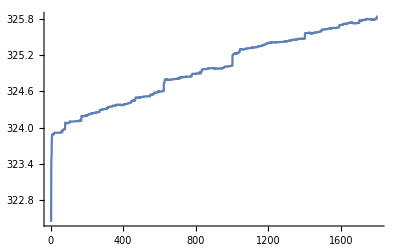

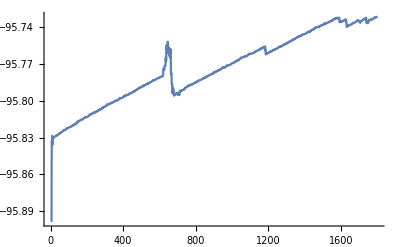

```mathematica
ListLinePlot[Table[ken[d,80]+pot[d,80],{d,hot}]]
ListLinePlot[Table[ken[d,80]+pot[d,80],{d,cold}]]
```

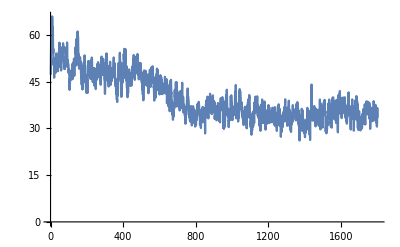

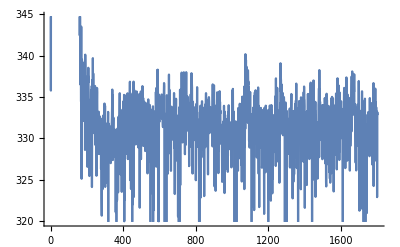

```mathematica
ListLinePlot[Table[ken[d,80],{d,cold}]]
ListLinePlot[Table[ken[d,80],{d,hot}]]
```

## Problem 2

### Part A

```mathematica
n=20;
```

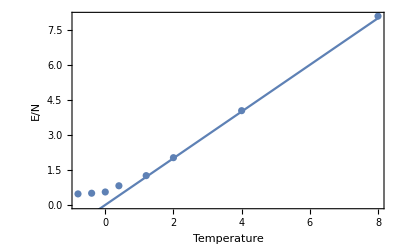

```mathematica
Needs["ErrorBarPlots`"]
epern={-0.8,-0.4,0,0.4,1.2,2.,4.,8.};
data=Partition[ReadList["p2_a.dat",Number],n*4+5];
therm=Table[ken[d,n],{d,data[[700;;]]}];
point1=Mean[therm];
sd1 = StandardDeviation[therm];
alpha1 = sd/Sqrt[Length[therm]];
data=Partition[ReadList["p2_b.dat",Number],n*4+5];
therm=Table[ken[d,n],{d,data[[700;;]]}];
point2=Mean[therm];
sd2 = StandardDeviation[therm];
alpha2 = sd/Sqrt[Length[therm]];
data=Partition[ReadList["p2_c.dat",Number],n*4+5];
therm =Table[ken[d,n],{d,data[[700;;]]}];
point3=Mean[therm];
sd3 = StandardDeviation[therm];
alpha3 = sd/Sqrt[Length[therm]];
data=Partition[ReadList["p2_d.dat",Number],n*4+5];
therm =Table[ken[d,n],{d,data[[700;;]]}];
point4=Mean[therm];
sd4 = StandardDeviation[therm];
alpha4 = sd/Sqrt[Length[therm]];
data=Partition[ReadList["p2_e.dat",Number],n*4+5];
therm = Table[ken[d,n],{d,data[[700;;]]}];
point5=Mean[therm];
sd5 = StandardDeviation[therm];
alpha5 = sd/Sqrt[Length[therm]];
data=Partition[ReadList["p2_f.dat",Number],n*4+5];
therm=Table[ken[d,n],{d,data[[700;;]]}];
point6=Mean[therm];
sd6 = StandardDeviation[therm];
alpha6 = sd/Sqrt[Length[therm]];
data=Partition[ReadList["p2_g.dat",Number],n*4+5];
therm = Table[ken[d,n],{d,data[[700;;]]}];
point7=Mean[therm];
sd7 = StandardDeviation[therm];
alpha7 = sd/Sqrt[Length[therm]];
data=Partition[ReadList["p2_h.dat",Number],n*4+5];
therm = Table[ken[d,n],{d,data[[700;;]]}];
point8=Mean[therm];
sd8 = StandardDeviation[therm];
alpha8 = sd/Sqrt[Length[therm]];

k=1;
igl=Plot[k*t,{t,-1,8}];
simpoint={point1, point2,point3,point4,point5,point6, point7, point8}/20;
errorbars={sd1,sd2,sd3,sd4,sd5,sd6,sd7,sd8}/Sqrt[Length[therm]];
errorplot= Table[{{epern[[i]],simpoint[[i]]},ErrorBar[errorbars[[i]]]},{i,Length[epern]}];
sim=ErrorListPlot[errorplot, Frame->True,FrameLabel->{"Temperature", "E/N"}];
Show[sim,igl]
```

### Part B

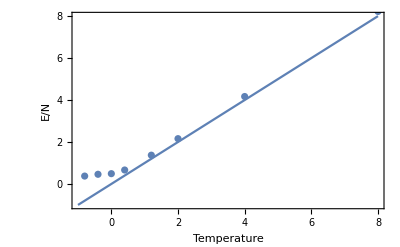

```mathematica
Needs["ErrorBarPlots`"]
epern={-0.8,-0.4,0,0.4,1.2,2.,4.,8.};
data=Partition[ReadList["p2b_a.dat",Number],n*4+5];
therm=Table[ken[d,n],{d,data[[700;;]]}];
point1=Mean[therm];
sd1 = StandardDeviation[therm];
alpha1 = sd/Sqrt[Length[therm]];
data=Partition[ReadList["p2b_b.dat",Number],n*4+5];
therm=Table[ken[d,n],{d,data[[700;;]]}];
point2=Mean[therm];
sd2 = StandardDeviation[therm];
alpha2 = sd/Sqrt[Length[therm]];
data=Partition[ReadList["p2b_c.dat",Number],n*4+5];
therm =Table[ken[d,n],{d,data[[700;;]]}];
point3=Mean[therm];
sd3 = StandardDeviation[therm];
alpha3 = sd/Sqrt[Length[therm]];
data=Partition[ReadList["p2b_d.dat",Number],n*4+5];
therm =Table[ken[d,n],{d,data[[700;;]]}];
point4=Mean[therm];
sd4 = StandardDeviation[therm];
alpha4 = sd/Sqrt[Length[therm]];
data=Partition[ReadList["p2b_e.dat",Number],n*4+5];
therm = Table[ken[d,n],{d,data[[700;;]]}];
point5=Mean[therm];
sd5 = StandardDeviation[therm];
alpha5 = sd/Sqrt[Length[therm]];
data=Partition[ReadList["p2b_f.dat",Number],n*4+5];
therm=Table[ken[d,n],{d,data[[700;;]]}];
point6=Mean[therm];
sd6 = StandardDeviation[therm];
alpha6 = sd/Sqrt[Length[therm]];
data=Partition[ReadList["p2b_g.dat",Number],n*4+5];
therm = Table[ken[d,n],{d,data[[700;;]]}];
point7=Mean[therm];
sd7 = StandardDeviation[therm];
alpha7 = sd/Sqrt[Length[therm]];
data=Partition[ReadList["p2b_h.dat",Number],n*4+5];
therm = Table[ken[d,n],{d,data[[700;;]]}];
point8=Mean[therm];
sd8 = StandardDeviation[therm];
alpha8 = sd/Sqrt[Length[therm]];

k=1;
igl=Plot[k*t,{t,-1,8}, Frame->True,FrameLabel->{"Temperature", "E/N"}];
simpoint={point1, point2,point3,point4,point5,point6, point7, point8}/20;
errorbars={sd1,sd2,sd3,sd4,sd5,sd6,sd7,sd8}/Sqrt[Length[therm]];
errorplot= Table[{{epern[[i]],simpoint[[i]]},ErrorBar[errorbars[[i]]]},{i,Length[epern]}];
sim=ErrorListPlot[errorplot];
Show[igl,sim]
```

## Problem 3

```mathematica
velocity[l_,n_]:=l[[2n+2;;4n+1]];
```

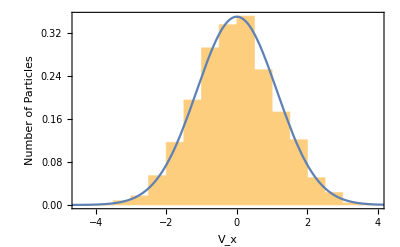

```mathematica
n = 40;
data=Partition[ReadList["p3_a.dat",Number],n*4+5];
therm = Table[ken[d,n],{d,data[[700;;]]}];
temp = Mean[therm]/n;
kex=Flatten[Table[velocity[d,n],{d,data[[700;;]]}]];
p2 = Histogram[kex,15,"PDF", Frame->True,FrameLabel->{"V_x","Number of Particles"}];
p1 = Plot[PDF[NormalDistribution[0,Sqrt[temp]],x]//Evaluate,{x,-6,6}];
Show[p2,p1]
```

```mathematica
V
```

40

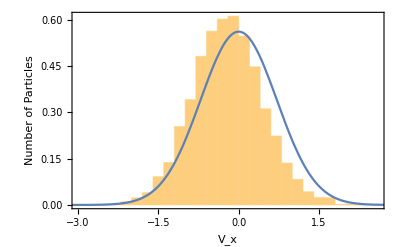

```mathematica
n = 40
data=Partition[ReadList["p3_b.dat",Number],n*4+5];
therm = Table[ken[d,n],{d,data[[400;;]]}];
temp = Mean[therm]/n;
kex=Flatten[Table[velocity[d,n],{d,data[[700;;]]}]];
p2 = Histogram[kex,30,"PDF", Frame->True,FrameLabel->{"V_x","Number of Particles"}];
p1 = Plot[PDF[NormalDistribution[0,Sqrt[temp]],x]//Evaluate,{x,-6,6}];
Show[p2,p1]
```

## Problem 4

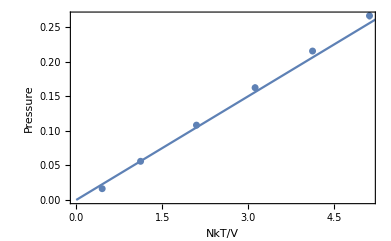

```mathematica
n = 20;

data=Partition[ReadList["p4_0.dat",Number],n*4+5];
pressure=Mean[Table[data[[-1,-i]]-data[[200,-i]],{i,4}]]/(180-20)/20;
errorpress = StandardDeviation[Table[data[[-1,-i]]-data[[200,-i]],{i,4}]]/(180-20)/20/Sqrt[4];
temp = Mean[Table[ken[d,n],{d,data[[500;;]]}]] /n;
errortemp = StandardDeviation[Table[ken[d,n],{d,data[[500;;]]}]] /n/Sqrt[n];
p0={{temp, pressure}, ErrorBar[errortemp, errorpress]};

data=Partition[ReadList["p4_1.dat",Number],n*4+5];
pressure=Mean[Table[data[[-1,-i]]-data[[200,-i]],{i,4}]]/(180-20)/20;
errorpress = StandardDeviation[Table[data[[-1,-i]]-data[[200,-i]],{i,4}]]/(180-20)/20/Sqrt[4];
temp = Mean[Table[ken[d,n],{d,data[[500;;]]}]] /n;
errortemp = StandardDeviation[Table[ken[d,n],{d,data[[500;;]]}]] /n/Sqrt[n];
p1={{temp, pressure}, ErrorBar[errortemp, errorpress]};

data=Partition[ReadList["p4_2.dat",Number],n*4+5];
pressure=Mean[Table[data[[-1,-i]]-data[[200,-i]],{i,4}]]/(180-20)/20;
errorpress = StandardDeviation[Table[data[[-1,-i]]-data[[200,-i]],{i,4}]]/(180-20)/20/Sqrt[4];
temp = Mean[Table[ken[d,n],{d,data[[500;;]]}]] /n;
errortemp = StandardDeviation[Table[ken[d,n],{d,data[[500;;]]}]] /n/Sqrt[n];
p2={{temp, pressure}, ErrorBar[errortemp, errorpress]};

data=Partition[ReadList["p4_3.dat",Number],n*4+5];
pressure=Mean[Table[data[[-1,-i]]-data[[200,-i]],{i,4}]]/(180-20)/20;
errorpress = StandardDeviation[Table[data[[-1,-i]]-data[[200,-i]],{i,4}]]/(180-20)/20/Sqrt[4];
temp = Mean[Table[ken[d,n],{d,data[[500;;]]}]] /n;
errortemp = StandardDeviation[Table[ken[d,n],{d,data[[500;;]]}]] /n/Sqrt[n];
p3={{temp, pressure}, ErrorBar[errortemp, errorpress]};

data=Partition[ReadList["p4_4.dat",Number],n*4+5];
pressure=Mean[Table[data[[-1,-i]]-data[[200,-i]],{i,4}]]/(180-20)/20;
errorpress = StandardDeviation[Table[data[[-1,-i]]-data[[200,-i]],{i,4}]]/(180-20)/20/Sqrt[4];
temp = Mean[Table[ken[d,n],{d,data[[500;;]]}]] /n;
errortemp = StandardDeviation[Table[ken[d,n],{d,data[[500;;]]}]] /n/Sqrt[n];
p4={{temp, pressure}, ErrorBar[errortemp, errorpress]};

data=Partition[ReadList["p4_5.dat",Number],n*4+5];
pressure=Mean[Table[data[[-1,-i]]-data[[200,-i]],{i,4}]]/(180-20)/20;
errorpress = StandardDeviation[Table[data[[-1,-i]]-data[[200,-i]],{i,4}]]/(180-20)/20/Sqrt[4];
temp = Mean[Table[ken[d,n],{d,data[[500;;]]}]] /n;
errortemp = StandardDeviation[Table[ken[d,n],{d,data[[500;;]]}]] /n/Sqrt[n];
p5={{temp, pressure}, ErrorBar[errortemp, errorpress]};
sim = ErrorListPlot[{p0,p1,p2,p3,p4, p5},AxesOrigin->{0,0}, Frame->True,FrameLabel->{"NkT/V", "Pressure"}];
theory = Plot[n*t/20^2,{t,0,5.25}];
Show[sim,theory]
```